# C - gaussian smear

## cosine trap switch, gaussian smear, plot <g|ρ|g> as a function of length scale of the smearing, with detector beginning in |g><g|

## set some parameters

```mathematica
α=1;
```

```mathematica
clear[λ];
```

```mathematica
Ω=1;
```

#### set values of σ; write σ in terms of σ_0~10^-4/Ω

```mathematica
σ0:=10^-4/Ω;
```

```mathematica
(*use these values for calculations*)
numSteps=200;
σMin=0.1 σ0;  σMax=2 σ0;  σStepSize=Abs[σMin-σMax]/numSteps;
σValues=Table[σ,{σ,σMin,σMax,σStepSize}];
```

```mathematica
(*then plot <g|ρ|g> versus σNorm=σ/Subscript[σ, 0]*)
σNormValues=σValues/σ0;
```

## the smearing function

```mathematica
f[x_,σ_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftil[k_,σ_]:=FourierTransform[f[x,σ],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

```mathematica
ftil[k,σ]
```

ⅇ^(-1/4 k^2 σ^2)

## the switching function

```mathematica
chiT1[t_]:=1/(r+T)1/2*(1+Cos[π/r(t+T/2)])
chiT2[t_]:=1/(r+T)
chiT3[t_]:=1/(r+T)1/2*(1+Cos[π/r(t-T/2)])
```

### the first interval

```mathematica
tpInt1[t_?NumericQ,k_?NumericQ]:=tpInt1[t,k]=NIntegrate[chiT1[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T-r,t}]
```

```mathematica
tInt1[k_?NumericQ]:=tInt1[k]=α*NIntegrate[chiT1[t] tpInt1[t,k],
{t,-T-r,-T}]
```

### the second interval

```mathematica
tpInt2[t_,k_]:=Integrate[chiT2[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T,t}]
```

```mathematica
tInt2[k_]:=α*Integrate[chiT2[t] tpInt2[t,k],
{t,-T,T}]
```

### the third interval

```mathematica
tpInt3[t_?NumericQ,k_?NumericQ]:=tpInt3[t,k]=NIntegrate[chiT3[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,T,t}]
```

```mathematica
tInt3[k_?NumericQ]:=tInt3[k]=α*NIntegrate[chiT3[t] tpInt3[t,k],
{t,T,T+r}]
```

## the k integrand

this integrand with the transition from Abs[k] → k taken into account (i.e. can now properly integrate from 0 to ∞ with proper factor of 2)

```mathematica
kIntegrand[k_,σ_]:=-1/π ⅇ^(-ε/2*k)*k*ftil[k,σ]^2*(tInt1[k]+tInt2[k]+tInt3[k])
```

## the numerical transition probability

```mathematica
T=2;r=0.2;Ω=1;
```

### with an ε regularized cutoff (exp)

```mathematica
ε=1/(5 Ω);
```

```mathematica
pexpG=Table[α+λ^2*NIntegrate[kIntegrand[k,σ],{k,0,∞}],{σ,σMin,σMax,σStepSize}];
```

```mathematica
pexpG10σ=α+λ^2*NIntegrate[kIntegrand[k,10 σ0],{k,0,∞}]
```

1-0.458654 λ^2

### with no cutoff (ε:=0)

```mathematica
ε=0;
```

```mathematica
pnoneG=Table[α+λ^2*NIntegrate[kIntegrand[k,σ],{k,0,∞}],{σ,σMin,σMax,σStepSize}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {4.81037×10^7}. NIntegrate obtained -0.620079 and 1.44385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {4.81037×10^7}. NIntegrate obtained -0.834047 and 1.15658 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {4.81037×10^7}. NIntegrate obtained -0.996162 and 0.937916 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

### with a sharp cutoff (ε:=0 and integrate only up to a constant)

```mathematica
ε=0;  cutoff=5*Ω;
```

```mathematica
psharpG=Table[α+λ^2*NIntegrate[kIntegrand[k,σ],{k,0,cutoff}],{σ,σMin,σMax,σStepSize}];
```

```mathematica
psharpG10σ=α+λ^2*NIntegrate[kIntegrand[k,10 σ0],{k,0,cutoff}]
```

1-0.455898 λ^2

## plot p v σ

```mathematica
λ=0.1;
```

#### put the data into lists for plotting

```mathematica
basePath="C:/Users/Public/Documents/emma/udw-detector-shape/Cosine Trap Switching/";
```

```mathematica
Export[FileNameJoin[{basePath,"SharpG10Sig.csv"}],psharpG10σ];
Export[FileNameJoin[{basePath,"ExpG10Sig.csv"}],pexpG10σ];
```

```mathematica
dataExpCutoffG     =Transpose[{σNormValues,pexpG}];
dataNoCutoffG       =Transpose[{σNormValues,pnoneG}];
dataSharpCutoffG=Transpose[{σNormValues,psharpG}];
```

```mathematica
Export[FileNameJoin[{basePath,"dataExpCutoffG.csv"}],dataExpCutoffG];
Export[FileNameJoin[{basePath,"dataNoCutoffG.csv"}],dataNoCutoffG];
Export[FileNameJoin[{basePath,"dataSharpCutoffG.csv"}],dataSharpCutoffG];
```

### ploot

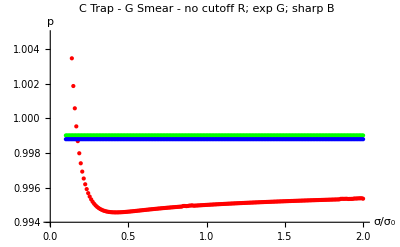

```mathematica
ListPlot[{dataNoCutoffG,dataExpCutoffG,dataSharpCutoffG},
AxesLabel->{σ/Subscript[σ, 0],p},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["C Trap - G Smear - no cutoff R; exp G; sharp B",FontSize->16]]
```

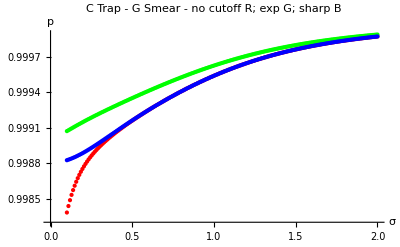

```mathematica
ListPlot[{dataNoCutoff,dataExpCutoff,dataSharpCutoff},
AxesLabel->{σ,p},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["C Trap - G Smear - no cutoff R; exp G; sharp B",FontSize->16]]
```

### make a plot for the amath mini-conference

```mathematica
ListPlot[{dataExpCutoff,dataExpCutoffL},
AxesLabel->{σ,p}];(*,
PlotLabel->Style["Probability of measuring ground state\n versus length scale of shape \n Gaussian shape blue, Lorentzian shape red",FontSize->16]]*)
```

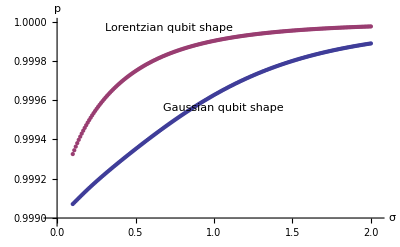

-Graphics-

### plot relative difference to p_δ